### Data Import

```mathematica
$HistoryLength=0
```

0

```mathematica
groundTruth=Import["/home/david/Desktop/Drexel_PhD/MATE T580/CERN Particle Tracking/train_100_events/event000001000-truth.csv"];
hits=Import["/home/david/Desktop/Drexel_PhD/MATE T580/CERN Particle Tracking/train_100_events/event000001000-hits.csv"];
cells=Import["/home/david/Desktop/Drexel_PhD/MATE T580/CERN Particle Tracking/train_100_events/event000001000-cells.csv"];
particles=Import["/home/david/Desktop/Drexel_PhD/MATE T580/CERN Particle Tracking/train_100_events/event000001000-particles.csv"];
```

```mathematica
groundTruth⟦;;10⟧//TableForm
```

hit_id | particle_id | tx | ty | tz | tpx | tpy | tpz | weight
1 | 0 | -64.4116 | -7.16412 | -1502.5 | 250710 | -149908 | -956385 | 0
2 | 22525763437723648 | -55.3385 | 0.630805 | -1502.5 | -0.570605 | 0.0283904 | -15.4922 | 9.86408×10^-6
3 | 0 | -83.828 | -1.14558 | -1502.5 | 626295 | -169767 | -760877 | 0
4 | 297237712845406208 | -96.1229 | -8.23036 | -1502.5 | -0.225235 | -0.0509684 | -3.70232 | 8.13311×10^-6
5 | 418835796137607168 | -62.6594 | -9.37504 | -1502.5 | -0.281806 | -0.023487 | -6.57318 | 8.87338×10^-6
6 | 108087696726949888 | -57.0856 | -8.18971 | -1502.5 | -0.401129 | -0.035276 | -10.4669 | 8.13311×10^-6
7 | 968286151951515648 | -73.8608 | -2.57586 | -1502.5 | -0.442662 | -0.0369686 | -9.1301 | 6.96788×10^-6
8 | 954766419537428480 | -63.8512 | -10.8754 | -1502.5 | -0.670459 | -0.0926088 | -15.5407 | 0.0000113644
9 | 707072769359085568 | -97.2489 | -10.9067 | -1502.5 | -0.279789 | -0.0621434 | -4.41292 | 8.13311×10^-6

```mathematica
hits⟦;;10⟧//TableForm
```

hit_id | x | y | z | volume_id | layer_id | module_id
1 | -64.4099 | -7.1637 | -1502.5 | 7 | 2 | 1
2 | -55.3361 | 0.635342 | -1502.5 | 7 | 2 | 1
3 | -83.8305 | -1.14301 | -1502.5 | 7 | 2 | 1
4 | -96.1091 | -8.24103 | -1502.5 | 7 | 2 | 1
5 | -62.6736 | -9.3712 | -1502.5 | 7 | 2 | 1
6 | -57.0687 | -8.17777 | -1502.5 | 7 | 2 | 1
7 | -73.8723 | -2.5789 | -1502.5 | 7 | 2 | 1
8 | -63.8535 | -10.8684 | -1502.5 | 7 | 2 | 1
9 | -97.2548 | -10.8891 | -1502.5 | 7 | 2 | 1

```mathematica
cells⟦;;10⟧//TableForm
```

hit_id | ch0 | ch1 | value
1 | 209 | 617 | 0.0138317
1 | 210 | 617 | 0.0798866
1 | 209 | 618 | 0.211723
2 | 68 | 446 | 0.334087
3 | 58 | 954 | 0.0340049
3 | 58 | 956 | 0.00779792
3 | 60 | 951 | 0.0198969
3 | 58 | 955 | 0.0999644
3 | 59 | 952 | 0.0655761

```mathematica
particles⟦;;10⟧//TableForm
```

particle_id | vx | vy | vz | px | py | pz | q | nhits
4503668346847232 | -0.00928816 | 0.00986098 | -0.0778789 | -0.0552689 | 0.323272 | -0.203492 | -1 | 8
4503737066323968 | -0.00928816 | 0.00986098 | -0.0778789 | -0.948125 | 0.470892 | 2.01006 | 1 | 11
4503805785800704 | -0.00928816 | 0.00986098 | -0.0778789 | -0.886484 | 0.105749 | 0.683881 | -1 | 0
4503874505277440 | -0.00928816 | 0.00986098 | -0.0778789 | 0.257539 | -0.676718 | 0.991616 | 1 | 12
4503943224754176 | -0.00928816 | 0.00986098 | -0.0778789 | 16.4394 | -15.5489 | -39.8249 | 1 | 3
4504011944230912 | -0.00928816 | 0.00986098 | -0.0778789 | 0.795277 | -1.6852 | -3.52089 | 1 | 12
4504080663707648 | -0.00928816 | 0.00986098 | -0.0778789 | -0.563433 | 0.30537 | 6.16712 | -1 | 14
4504355541614592 | -0.00928816 | 0.00986098 | -0.0778789 | -0.501267 | 0.0498246 | -0.213011 | -1 | 17
4504424261091328 | -0.00928816 | 0.00986098 | -0.0778789 | -1.65212 | 0.453142 | -0.533958 | -1 | 12

### Sample Particle Trajectory

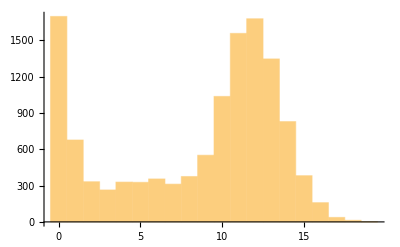

```mathematica
Histogram[particles⟦2;;,-1⟧]
```

```mathematica
Select[particles,#⟦-1⟧≥18&]
```

{{4550397591027712,6.0757,-3.01828,-1.65696,7.38497,-3.59907,-1.75212,1,18},{58548032106397696,0.0081656,-0.00385015,-1.2045,0.27453,-0.104014,0.185207,1,18},{94586999607918592,0.00375047,0.0105381,6.9397,0.503882,0.22477,0.287038,1,18},{117103142318899200,0.000486502,-0.00918186,0.208295,-0.345216,-0.08869,-0.00177034,-1,18},{139613718752264192,-0.0455581,-0.00213868,8.45589,0.482294,-0.0503626,4.07837,1,18},{153125410987573248,-0.000420138,0.0270689,1.76687,-0.313087,0.102564,-0.0449077,1,19},{220699677643767808,-0.0215424,0.00567734,-4.09596,-0.133632,0.390753,0.468328,1,18},{436849851049705472,-0.0162173,-0.0286304,2.15441,0.204892,-0.845048,5.65434,1,18},{445859318047178752,0.000836314,-0.0021718,-5.04407,-2.43863,0.976885,-12.1953,-1,18},{499903200770392064,0.00597668,-0.00744874,-5.06495,-0.113335,0.230245,0.0376614,1,18},{571958733240799233,-17.9668,6.18002,397.053,-0.307351,0.0316048,-0.0131079,1,19},{662037322841194496,-0.000737204,-0.00617908,-10.0669,0.193805,0.201552,0.26713,1,18},{671041361000005632,0.00214885,0.0106571,-2.2711,0.52302,0.76019,-7.94179,1,18},{734093542489587712,-0.00916967,-0.00476335,-2.64611,0.376105,0.0269405,-1.00549,1,18},{797159948927651842,-18.9996,-0.124314,116.617,-0.196404,-0.017048,1.30722,1,18}}

```mathematica
Table[Select[groundTruth,#⟦2⟧==i&]⟦;;,{3,4,5}⟧,{i,Select[particles,#⟦-1⟧≥19&]⟦;;,1⟧}]
```

{{{-30.1961,10.9005,-2.59771},{-31.3448,11.354,-2.76405},{-66.3432,26.8882,-7.9248},{-68.0849,27.7396,-8.18918},{-105.775,48.5117,-14.2136},{-151.798,79.6203,-22.3252},{-153.427,80.854,-22.6226},{-219.679,140.537,-35.6219},{-284.468,224.683,-51.0638},{-281.001,219.255,-50.1468},{-286.065,227.212,-51.4883},{-282.647,221.822,-50.5851},{-347.053,362.449,-73.0456},{-345.256,356.291,-72.1652},{-366.198,551.504,-99.2306},{-366.748,544.364,-98.2844},{-305.476,758.114,-127.761},{49.8617,1022.43,-186.905},{34.6845,1018.94,-184.862}},{{-31.5477,7.75673,396.473},{-70.1931,14.2054,394.352},{-72.2179,14.6274,394.238},{-114.166,25.318,392.231},{-166.064,43.6222,390.071},{33.0952,82.3993,1497.5},{18.2961,79.4475,1502.5},{-249.284,87.3212,386.958},{-327.623,148.884,382.88},{-423.986,272.898,377.884},{-420.92,267.529,378.066},{-482.683,454.565,371.822},{-451.069,691.217,364.078},{-454.633,682.202,364.273},{-133.563,1010.75,1078.32},{359.764,773.929,1217.5},{-604.83,601.636,1794.5},{-604.874,625.245,1802.5},{-604.975,610.657,1797.5}}}

```mathematica
ListPointPlot3D[Select[groundTruth,#⟦2⟧==153125410987573248&]⟦;;,{3,4,5}⟧,AspectRatio->1]/.Point[a___]:>{Thick,Red,Line[a],Blue,Point[a]}
```

-Graphics3D-

### Detector Visualization

```mathematica
detectors=Import["/home/david/Desktop/Drexel_PhD/MATE T580/CERN Particle Tracking/detectors.csv"]
```

{{volume_id,layer_id,module_id,cx,cy,cz,rot_xu,rot_xv,rot_xw,rot_yu,rot_yv,rot_yw,rot_zu,rot_zv,rot_zw,module_t,module_minhu,module_maxhu,module_hv,pitch_u,pitch_v},{7,2,1,-65.7965,-5.1783,-1502.5,0.0784591,-0.996917,0,-0.996917,-0.0784591,0,0,0,-1,0.15,8.4,8.4,36,0.05,0.05625},{7,2,2,-139.851,-6.46568,-1502,0.0461835,-0.998933,0,-0.998933,-0.0461835,0,0,0,-1,0.15,8.4,8.4,36,0.05,0.05625},18724,{18,12,97,-826.227,54.1538,2944.5,0.0654031,-0.997859,0,0.997859,0.0654031,0,0,0,1,0.35,54,64.2,78,0.12,10.4},{18,12,98,-940.141,59.1487,2952.5,0.0627905,-0.998027,0,0.998027,0.0627905,0,0,0,1,0.35,66,72,78,0.12,10.4}}
 |  |  |  |

```mathematica
detectors⟦;;10⟧//TableForm
```

volume_id | layer_id | module_id | cx | cy | cz | rot_xu | rot_xv | rot_xw | rot_yu | rot_yv | rot_yw | rot_zu | rot_zv | rot_zw | module_t | module_minhu | module_maxhu | module_hv | pitch_u | pitch_v
7 | 2 | 1 | -65.7965 | -5.1783 | -1502.5 | 0.0784591 | -0.996917 | 0 | -0.996917 | -0.0784591 | 0 | 0 | 0 | -1 | 0.15 | 8.4 | 8.4 | 36 | 0.05 | 0.05625
7 | 2 | 2 | -139.851 | -6.46568 | -1502 | 0.0461835 | -0.998933 | 0 | -0.998933 | -0.0461835 | 0 | 0 | 0 | -1 | 0.15 | 8.4 | 8.4 | 36 | 0.05 | 0.05625
7 | 2 | 3 | -138.657 | -19.3419 | -1498 | 0.138156 | -0.99041 | 0 | -0.99041 | -0.138156 | 0 | 0 | 0 | -1 | 0.15 | 8.4 | 8.4 | 36 | 0.05 | 0.05625
7 | 2 | 4 | -64.1764 | -15.4074 | -1498 | 0.233445 | -0.97237 | 0 | -0.97237 | -0.233445 | 0 | 0 | 0 | -1 | 0.15 | 8.4 | 8.4 | 36 | 0.05 | 0.05625
7 | 2 | 5 | -136.281 | -32.0531 | -1502 | 0.228951 | -0.973438 | 0 | -0.973438 | -0.228951 | 0 | 0 | 0 | -1 | 0.15 | 8.4 | 8.4 | 36 | 0.05 | 0.05625
7 | 2 | 6 | -60.976 | -25.2571 | -1502 | 0.382683 | -0.92388 | 0 | -0.92388 | -0.382683 | 0 | 0 | 0 | -1 | 0.15 | 8.4 | 8.4 | 36 | 0.05 | 0.05625
7 | 2 | 7 | -132.742 | -44.4908 | -1498 | 0.317791 | -0.948161 | 0 | -0.948161 | -0.317791 | 0 | 0 | 0 | -1 | 0.15 | 8.4 | 8.4 | 36 | 0.05 | 0.05625
7 | 2 | 8 | -128.071 | -56.5489 | -1502 | 0.403921 | -0.914794 | 0 | -0.914794 | -0.403921 | 0 | 0 | 0 | -1 | 0.15 | 8.4 | 8.4 | 36 | 0.05 | 0.05625
7 | 2 | 9 | -56.2743 | -34.4849 | -1497.5 | 0.522499 | -0.85264 | 0 | -0.85264 | -0.522499 | 0 | 0 | 0 | -1 | 0.15 | 8.4 | 8.4 | 36 | 0.05 | 0.05625

```mathematica
Graphics3D[Cuboid[#⟦4;;6⟧,#⟦4;;6⟧+#⟦{16,17,19}⟧]&/@detectors⟦2;;⟧]
```

-Graphics3D-

```mathematica
Show[
Graphics3D[Cuboid[#⟦4;;6⟧,#⟦4;;6⟧+#⟦{16,17,19}⟧]&/@detectors⟦2;;⟧],ListPointPlot3D[Table[Select[groundTruth,#⟦2⟧==i&]⟦;;,{3,4,5}⟧,{i,Select[particles,#⟦-1⟧==16&]⟦;;,1⟧}],AspectRatio->1]/.Point[a___]:>{Thick,Red,Line[a],Blue,Point[a]}
]
```

```mathematica
trajX=(ListPlot[Table[Select[groundTruth,#⟦2⟧==i&]⟦;;,{4,5}⟧,{i,Select[particles,#⟦-1⟧==16&]⟦;;,1⟧}],PlotRange->Full,AspectRatio->1]/.Point[a___]:>{Thick,Red,Line[a],Blue,Point[a]});
trajY=(ListPlot[Table[Select[groundTruth,#⟦2⟧==i&]⟦;;,{3,5}⟧,{i,Select[particles,#⟦-1⟧==16&]⟦;;,1⟧}],PlotRange->Full,AspectRatio->1]/.Point[a___]:>{Thick,Red,Line[a],Blue,Point[a]});
trajZ=(ListPlot[Table[Select[groundTruth,#⟦2⟧==i&]⟦;;,{3,4}⟧,{i,Select[particles,#⟦-1⟧==16&]⟦;;,1⟧}],PlotRange->Full,AspectRatio->1]/.Point[a___]:>{Thick,Red,Line[a],Blue,Point[a]});

detectorGraphics=Graphics3D[Cuboid[#⟦4;;6⟧,#⟦4;;6⟧+#⟦{16,17,19}⟧]&/@detectors⟦2;;⟧];
```

```mathematica
xbound=1000;
zbound=3000;
trX=Graphics3D[
{Texture[trajX],
EdgeForm[],
Opacity[0.8],
Lighting->"Neutral",
Polygon[{{xbound,-xbound,-zbound},{xbound,xbound,-zbound},{xbound,xbound,zbound},{xbound,-xbound,zbound}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}],
ImageSize->2000}];
trY=Graphics3D[
{Texture[trajY],
EdgeForm[],
Opacity[0.8],
Lighting->"Neutral",
Polygon[{{-xbound,xbound,-zbound},{xbound,xbound,-zbound},{xbound,xbound,zbound},{-xbound,xbound,zbound}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}],
ImageSize->2000}];
trZ=Graphics3D[
{Texture[trajZ],
EdgeForm[],
Opacity[0.8],
Lighting->"Neutral",
Polygon[{{-xbound,-xbound,-zbound},{xbound,-xbound,-zbound},{xbound,xbound,-zbound},{-xbound,xbound,-zbound}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}],
ImageSize->2000}];
```

```mathematica
Show[detectorGraphics,trX,trY,trZ,ViewPoint->{-10^4,-10^4,10^4},ViewVertical->{0,0,1}]
```

### Track Cluster Analysis

```mathematica
Table[Select[groundTruth,#⟦2⟧==i&]⟦;;,{4,5}⟧,{i,Select[particles,#⟦-1⟧==16&]⟦;;,1⟧}]
```

{{{-13.4363,0.303117},{-13.9803,0.317883},{-13.2306,0.297419},{-13.766,0.312125},{-30.12,0.761617},{-29.9174,0.75581},{-46.8877,1.21944},{-67.5136,1.87738},{-68.2111,1.89976},{-99.0087,3.12569},{-129.764,4.40288},{-166.532,6.43417},{-199.764,9.13776},{-198.754,9.03354},{-220.909,11.9027},{-233.832,15.4645}},157,{{70.0034,-1502},{69.7916,-1497.5},{60.5975,-1302},{60.3864,-1297.5},{51.2313,-1102},{51.0209,-1097.5},{44.6814,-962},{44.4714,-957.5},{38.1591,-822},{37.95,-817.5},{32.4101,-698},{32.5955,-702},{32.3869,-697.5},{27.7805,-598},{27.9658,-602},{27.7573,-597.5}}}
 |  |  |  |

```mathematica
tracks=GatherBy[groundTruth⟦2;;⟧,#⟦2⟧&]⟦2;;⟧
```

{1}
 |  |  |  |

```mathematica
t1=RandomSample[tracks,10];
t2=RandomSample[tracks,100];
t3=RandomSample[tracks,1000];
```

#### No coordinate transformation

```mathematica
ListPointPlot3D[({#⟦3⟧,#⟦4⟧,#⟦5⟧}&/@#)&/@t1]/.Point[a___]:>{Thick,Line[a],Point[a]}
```

-Graphics3D-

```mathematica
ListPointPlot3D[({#⟦3⟧,#⟦4⟧,#⟦5⟧}&/@Sort[#])&/@t2]/.Point[a___]:>{Thick,Line[a],Point[a]}
```

-Graphics3D-

```mathematica
ListPointPlot3D[({#⟦3⟧,#⟦4⟧,#⟦5⟧}&/@#)&/@t3]/.Point[a___]:>{Thick,Line[a],Point[a]}
```

-Graphics3D-

#### Helical coordinate transformation

Used in the baseline DBSCAN benchmark.

x_1==x/(√(x^2+y^2+z^2))

y_1==y/(√(x^2+y^2+z^2))

z_1==x/(√(x^2+y^2))

```mathematica
ListPointPlot3D[({(#⟦3⟧)/(√((#⟦3⟧)^2+(#⟦4⟧)^2+(#⟦5⟧)^2)),(#⟦4⟧)/(√((#⟦3⟧)^2+(#⟦4⟧)^2+(#⟦5⟧)^2)),(#⟦5⟧)/(√((#⟦3⟧)^2+(#⟦4⟧)^2))}&/@Sort[#])&/@t1]/.Point[a___]:>{Thick,Line[a],Point[a]}
```

-Graphics3D-

```mathematica
ListPointPlot3D[({(#⟦3⟧)/(√((#⟦3⟧)^2+(#⟦4⟧)^2+(#⟦5⟧)^2)),(#⟦4⟧)/(√((#⟦3⟧)^2+(#⟦4⟧)^2+(#⟦5⟧)^2)),(#⟦5⟧)/(√((#⟦3⟧)^2+(#⟦4⟧)^2))}&/@Sort[#])&/@t2]/.Point[a___]:>{Thick,Line[a],Point[a]}
```

-Graphics3D-

```mathematica
ListPointPlot3D[({(#⟦3⟧)/(√((#⟦3⟧)^2+(#⟦4⟧)^2+(#⟦5⟧)^2)),(#⟦4⟧)/(√((#⟦3⟧)^2+(#⟦4⟧)^2+(#⟦5⟧)^2)),(#⟦5⟧)/(√((#⟦3⟧)^2+(#⟦4⟧)^2))}&/@Sort[#])&/@t3]/.Point[a___]:>{Thick,Line[a],Point[a]}
```

-Graphics3D-

#### Custom coordinate transformation #1

x_1==x/(z √(x^2+y^2+z^2))

y_1==y/(z √(x^2+y^2+z^2))

z_1==x/(√(x^2+y^2))

```mathematica
?ArcTan
```

ArcTan[z] gives the arc tangent tan^-1(z) of the complex number z. 
ArcTan[x,y] gives the arc tangent of y/x, taking into account which quadrant the point (x,y) is in.